```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/developer3/git/Networks

```mathematica
tshirt = Import["./soccer18.eps"]
```

-Graphics-

Show::gtype: Symbol is not a type of graphics. ButtonBox["»",
Appearance->{Automatic, None},
BaseStyle->"Link",
ButtonData:>"paclet:ref/message/Show/gtype",
ButtonNote->"Show::gtype"]

```mathematica
getIcon[player_]:= player["playerNumber"]-> Show[Rasterize[Show[tshirt , Prolog -> Inset[Show[CountryData[player["country"], "Flag"], ImageSize -> {500,500}]], Epilog->Inset[Row[{Style[player["playerName"],60, Bold],Style["\n"<>ToString[player["playerNumber"]],150, Bold] }] ,{Center,200}]]],ImageSize->{85,45},AspectRatio->Full];
```

```mathematica
data = {
<|"playerName"->"Messi", "playerNumber" -> 10, "country" ->  "Argentina"|> ,
<|"playerName"->"Adrian", "playerNumber" -> 11, "country" -> "Argentina"|> ,
<|"playerName"->"Felipe", "playerNumber" -> 12, "country" -> "Argentina"|> 
};
```

Global`data

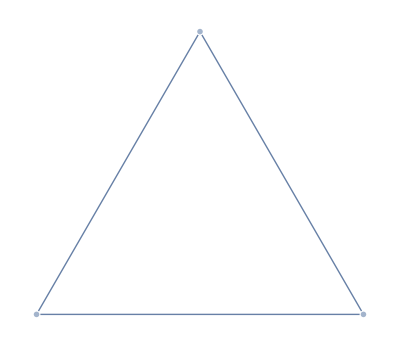

```mathematica
Graph[{10 <-> 11, 11 <-> 12, 12 <-> 10},VertexSize->0.15 , VertexShape -> getIcon /@ data]
```